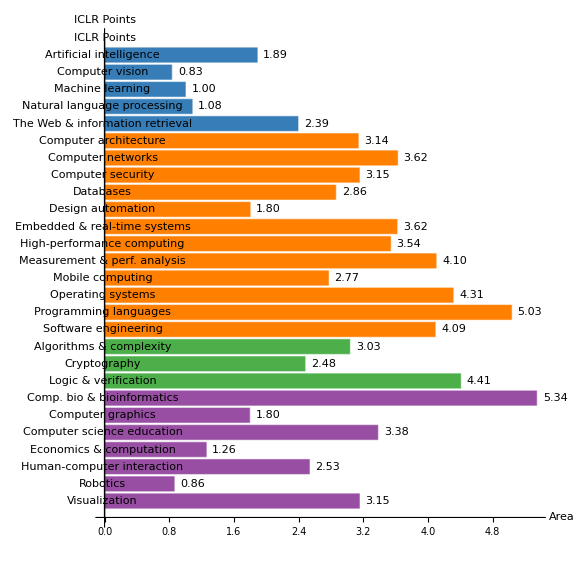

```mathematica
(*Import names.csv and build a mapping:ParentArea->{ReadableTitle,ParentParentArea}*)namesData=Import[FileNameJoin[{NotebookDirectory[],"conferences.csv"}],"CSV"];
namesData=Rest[namesData];  (*remove header row*)
areaMapping=Association[Table[namesData[[i,3]]->{namesData[[i,4]],namesData[[i,5]]},{i,Length[namesData]}]];

(*Import the publication data*)
data=Import[FileNameJoin[{NotebookDirectory[],"iclr.csv"}],"CSV"];
data=Rest[data];  (*remove header row*)
areas=data[[All,1]];
iclrPoints=ToExpression[data[[All,5]]];

(*Map each ParentArea to its readable title and parent parent area*)
mapped=areaMapping/@areas;
readableTitles=mapped[[All,1]];
parentParent=mapped[[All,2]];

(*Define a unique color for each ParentParentArea*)
colorMapping=<|"AI"->RGBColor[55/255,126/255,184/255],"Systems"->RGBColor[255/255,127/255,0/255],"Theory"->RGBColor[77/255,175/255,74/255],"Interdisciplinary Areas"->RGBColor[152/255,78/255,163/255]|>;
barColors=Lookup[colorMapping,parentParent,Gray];

(*Define desired order for ParentParentArea*)
order={"AI","Systems","Theory","Interdisciplinary Areas"};
sortKey[pp_]:=FirstPosition[order,pp,{Infinity}][[1]];

(*Combine and sort the data based on ParentParentArea order*)
combined=Transpose[{readableTitles,iclrPoints,parentParent,barColors}];
sortedCombined=SortBy[combined,sortKey[#[[3]]]&];
sortedReadable=sortedCombined[[All,1]];
sortedICLRPoints=sortedCombined[[All,2]];
sortedBarColors=sortedCombined[[All,4]];

(*Create a horizontal bar chart*)
BarChart[Reverse@sortedICLRPoints,LabelingFunction->(Placed[NumberForm[#1,{4,2}],After]&),AspectRatio->1,BarOrigin->Left,ChartLabels->Reverse@sortedReadable,ChartStyle->Reverse@sortedBarColors,AxesLabel->{"ICLR Points","Area"},ImageSize->Large]
```

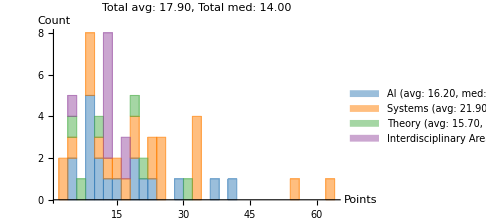

```mathematica
(*Define the desired order and color mapping*)order={"AI","Systems","Theory","Interdisciplinary Areas"};
colorMapping=<|"AI"->RGBColor[55/255,126/255,184/255],"Systems"->RGBColor[255/255,127/255,0/255],"Theory"->RGBColor[77/255,175/255,74/255],"Interdisciplinary Areas"->RGBColor[152/255,78/255,163/255]|>;

(*Import the CSV file;update the path as needed*)
data=Import[FileNameJoin[{NotebookDirectory[],"candidate_iclr.csv"}],"CSV"];
rawData=Rest[data];  (*drop header*)

(*Group data by parent_parent_area (column 5)*)
grouped=GroupBy[rawData,#[[5]]&];

(*Reorder groups using the defined order*)
sortedKeys=Select[order,MemberQ[Keys[grouped],#]&];

(*Extract first-author ICLR points (column 2) for each group in sorted order;
convert them to numbers*)
pointsList=Map[ToExpression/@(#[[2]]&/@#)&,grouped];
sortedPointsList=Lookup[pointsList,sortedKeys];

(*Compute average and median for each area*)
areaAverages=Map[Mean,sortedPointsList];
areaMedians=Map[Median,sortedPointsList];

(*Aggregate data across all areas*)
allData=Flatten[sortedPointsList];
allDataPos=Select[allData,#>0&];  (*for LogNormal fit*)

(*Compute overall average and median*)
totalAvg=Mean[allDataPos];
totalMedian=Median[allDataPos];

(*Generate legend entries for each area including average and median*)
legendEntries=MapThread[#1<>" \n(avg: "<>ToString[NumberForm[#2,{3,2}]]<>", med: "<>ToString[NumberForm[#3,{3,2}]]<>")"&,{sortedKeys,areaAverages,areaMedians}];

(*Create a stacked histogram with 1-unit bin width and density normalization*)
stackedHistogram=Histogram[sortedPointsList,20,ChartLayout->"Stacked",ChartLegends->Placed[legendEntries,{0.75,0.95}],ChartStyle->(Lookup[colorMapping,#,Gray]&/@sortedKeys),AxesLabel->{"Points","Count"},PlotLabel->"Total avg: "<>ToString[NumberForm[totalAvg,{3,2}]]<>", Total med: "<>ToString[NumberForm[totalMedian,{3,2}]],ImageSize->Medium];

stackedHistogram
```

```mathematica
(*Define the data and corresponding labels*)data={232,21,139,21,231,2};
labels={"North America","South America","Asia","Australasia","Europe","Africa"};

(*Create the pie chart with RadialCallout labels and a legend*)
PieChart[data,ChartLabels->Placed[MapThread[#1<>" ("<>ToString[#2]<>")"&,{labels,data}],"VerticalCallout"],ChartStyle->"Pastel",ImageSize->Medium,ImagePadding->{{100,80},{Automatic,Automatic}}]
```

-Graphics-

```mathematica
(*Import the CSV file*)data=Import[FileNameJoin[{NotebookDirectory[],"faculty_iclr_details.csv"}],"CSV"];
```

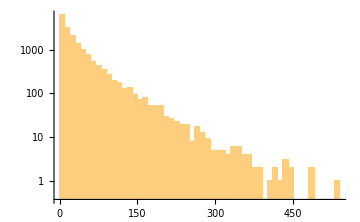

```mathematica
(*Remove header row*)
rows=Rest[data];

(*Extract the count values (fifth column)*)
counts=rows[[All,5]];

hist=Histogram[counts,40,ScalingFunctions->"Log",PlotRange->All,ImageSize->Medium]
```

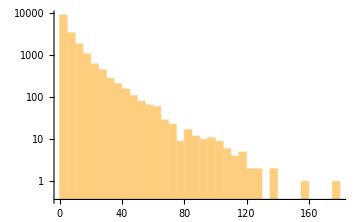

```mathematica
(*Remove header row*)
rows=Rest[data];

(*Extract the count values (fifth column)*)
counts=rows[[All,6]];

hist=Histogram[counts,40,ScalingFunctions->"Log",PlotRange->All,ImageSize->Medium]
```

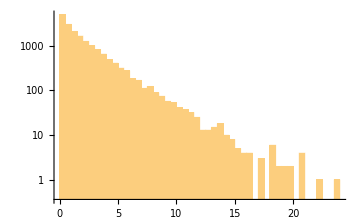

```mathematica
(*Remove header row*)
rows=Rest[data];

(*Extract the count values (fifth column)*)
counts=rows[[All,7]];

hist=Histogram[counts,40,ScalingFunctions->"Log",PlotRange->All,ImageSize->Medium]
```

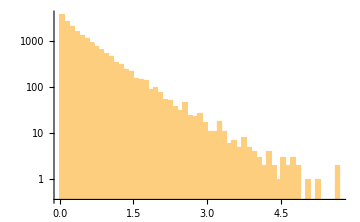

```mathematica
(*Remove header row*)
rows=Rest[data];

(*Extract the count values (fifth column)*)
counts=rows[[All,8]];

hist=Histogram[counts,40,ScalingFunctions->"Log",PlotRange->All,ImageSize->Medium]
```

```mathematica
(*Import the CSV data*)data=Import["institute_adjusted_details.csv","CSV"];

(*The first row contains headers;separate it from the data rows*)
headers=First[data];
dataRows=Rest[data];

(*Build an association:institute-><|area->AdjustedICLRPoints|>*)
instituteAssoc=Association[];
Do[With[{inst=row[[1]],area=row[[2]],points=ToExpression[row[[3]]]},If[KeyExistsQ[instituteAssoc,inst],instituteAssoc[inst][area]=points,instituteAssoc[inst]=<|area->points|>]],{row,dataRows}];

(*Define sorted categories (use 0 for categories that have no data)*)
categories={"ai","vision","mlmining","nlp","inforet","arch","comm","sec","mod","da","bed","hpc","mobile","metrics","ops","plan","soft","act","crypt","log","bio","graph","csed","ecom","chi","robotics","visualization"};

(*Function to extract a data vector for a given institute*)
getData[institute_]:=Module[{assoc,values},assoc=Lookup[instituteAssoc,institute,<||>];
values=Table[If[KeyExistsQ[assoc,cat],assoc[cat],0],{cat,categories}];
values];

(*List of institute names to plot*)
institutes={"Zhejiang University","KAIST"};

(*Obtain data vectors for the selected institutes*)
dataVectors=getData/@institutes;

(*Create the radar chart for comparison.(Assuming RadialAxisPlot is defined or available in your environment.)*)
RadialAxisPlot[dataVectors,AxesLabel->categories,PlotLegends->Placed[institutes,Bottom],ImageSize->Medium,Filling->False]
```

-Graphics-